Here are both of our defined funnels, where f1 is the 1-Dimensional funnel and mullerBrown is our 2-Dimensional folding funnel

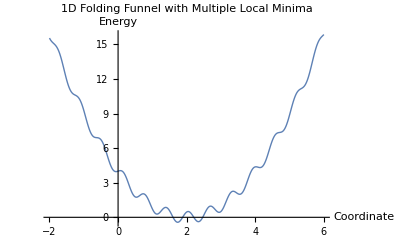

-Graphics-

-Graphics3D-

{-146.7,{x→-0.558224,y→1.44173}}

Global minimum value: -146.7

Position of global minimum: {x = -0.558224, y = 1.44173}

```mathematica
f1[x_]:=(x-2)^2+0.5 Sin[10 x]
mullerBrown[x_,y_]:=-200*Exp[-1*(x-1)^2-10*(y-0)^2]+-100*Exp[-1*(x-0)^2-10*(y-0.5)^2]+-170*Exp[-6.5*(x+0.5)^2+11*(x+0.5)*(y-1.5)-6.5*(y-1.5)^2]+15*Exp[0.7*(x+1)^2+0.6*(x+1)*(y-1)+0.7*(y-1)^2];

Plot[f1[x],{x,-2,6},PlotLabel->"1D Folding Funnel with Multiple Local Minima",AxesLabel->{"Coordinate","Energy"},PlotStyle->Thick]
ContourPlot[mullerBrown[x,y],{x,-1.5,1.5},{y,-0.5,2.0},PlotRange->{-150,100},Contours->30,ContourLines->True,ColorFunction->"ThermometerColors",PlotLegends->Automatic,FrameLabel->{"x","y"},PlotLabel->"Müller-Brown Potential Energy Surface",ImageSize->Large,PlotPoints->100]

Plot3D[mullerBrown[x,y],{x,-1.5,1.5},{y,-0.5,2.0},PlotRange->{-150,100},ColorFunction->"ThermometerColors",AxesLabel->{"x","y","Energy"},PlotLabel->"Müller-Brown Potential Energy Surface",ViewPoint->{1.3,-2.4,2.0},ImageSize->Large,PlotPoints->100,MaxRecursion->4,MeshFunctions->{#3&},Mesh->15]
(*Find the global minimum to verify minimization methods*)globalMin=NMinimize[{mullerBrown[x,y],-1.5<=x<=1.5,-0.5<=y<=2.0},{x,y}]

Print["Global minimum value: ",globalMin[[1]]]
Print["Position of global minimum: {x = ",globalMin[[2,1,2]],", y = ",globalMin[[2,2,2]],"}"]
```

Here we test out Newton’s method in the 1-dimensional function:

```mathematica
FindMinimum[f1[x],{x,1.5},Method->"Newton"]
FindMinimum[f1[x],{x,0},Method->"Newton"]
```

{-0.428799,{x→1.73836}}

{3.96128,{x→-0.0602206}}

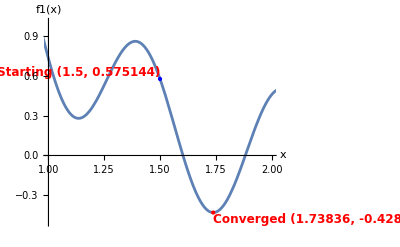

```mathematica
start={1.5,f1[1.5]};
conv={1.7383607296496955,f1[1.7383607296496955]};

Plot[f1[x],{x,-2,4},PlotRange->{{1,2},{-0.5,1}},(*Adjust these ranges as needed*)AxesLabel->{"x","f1(x)"},Epilog->{Blue,PointSize[Large],Point[start],Red,PointSize[Large],Point[conv],Text[Style["Starting ("<>ToString[N[start[[1]],4]]<>", "<>ToString[N[start[[2]],4]]<>")",Bold,12],start,{1,-1}],Text[Style["Converged ("<>ToString[N[conv[[1]],4]]<>", "<>ToString[N[conv[[2]],4]]<>")",Bold,12],conv,{-1,1}]}]
```

Here we tested Newton’s method on the 2-dimensional funnel:

```mathematica
steps1 = 0
result1 = FindMinimum[mullerBrown[x, y], {{x,-1},{y,1}}, Method->"Newton", StepMonitor:>(steps1++)]
steps1
```

0

{-146.7,{x→-0.558224,y→1.44173}}

5

Here we test the conjugate gradient method with the 1D function:

```mathematica
FindMinimum[f1[x],{x,0},Method->{"ConjugateGradient"}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{3.96128,{x→-0.0602206}}

Here we test the conjugate gradient method with the Muller function:

```mathematica
steps2 = 0
result = FindMinimum[mullerBrown[x, y], {{x,-1},{y,1}}, Method->"ConjugateGradient", StepMonitor:>(steps2++)] (*Testing out number of steps algorithm took*)
steps2
```

0

{-146.7,{x→-0.558224,y→1.44173}}

9

Testing out Simulated Annealing:

```mathematica
NMinimize[f1[x],{x},Method->"SimulatedAnnealing"]
NMinimize[mullerBrown[x,y],{x,y},Method->"SimulatedAnnealing"]
NMinimize[mullerBrown[x,y],{x,y},Method->{"SimulatedAnnealing","PerturbationScale"->0.4}]
```

{-0.428799,{x→1.73836}}

{-108.167,{x→0.623499,y→0.0280378}}

{-146.7,{x→-0.558224,y→1.44173}}

Testing out Differential Evolution

```mathematica
NMinimize[f1[x],{x},Method->"DifferentialEvolution"]
NMinimize[mullerBrown[x,y],{x,y},Method->"DifferentialEvolution"]
```

{-0.428799,{x→1.73836}}

{-146.7,{x→-0.558224,y→1.44173}}

Testing out random search

```mathematica
NMinimize[f1[x],{x},Method->"RandomSearch"]
NMinimize[mullerBrown[x,y],{x,y},Method->"RandomSearch"]
```

{-0.428799,{x→1.73836}}

{-146.7,{x→-0.558224,y→1.44173}}